## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="RBPC";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data_PE.csv";

mainFolder = "fit_RUBISCO_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:C:\MASSef\examples\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(co2^c+h2o^c+rb15bp^c→2 (3pg)^c+2 h^c)^RBPC

Ordered Bi Bi; [rb15bp, co2, 3pg, 3pg]

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | rb15bp | Null
co2 | Null | 400000 | 380000.
420000. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | co2 | 0.00001 | 9.5×10^-6
0.0000105 |  | M | 7.4 | 25 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1
1 | rb15bp | 0.00005 | 0.0000475
0.0000525 | amp | 0.001 | M | 7.4 | 25 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | rb15bp | Null
co2 | Null | 45.0422 | 42.7901
47.2943 | 1/s | 7.4 | 37 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(co2^c+h2o^c+rb15bp^c→2 (3pg)^c+2 h^c)^RBPC

Ordered Bi Bi; [rb15bp, co2, 3pg, 3pg]

Structure: 1

Active sites: 1

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | rb15bp | Null
co2 | Null | 400000 | 380000.
420000. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | co2 | 0.00001 | 9.5×10^-6
0.0000105 |  | M | 7.4 | 25 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1
1 | rb15bp | 0.00005 | 0.0000475
0.0000525 | amp | 0.001 | M | 7.4 | 25 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | rb15bp | Null
co2 | Null | 45.0422 | 42.7901
47.2943 | 1/s | 7.4 | 37 | trishcl | 0.05 | mg2 | 0.002
cl | 0.004
cl | 0.1
k | 0.1

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_RBPC[c] + rb15bp[c] <=> E_RBPC[c]&rb15bp",
				"E_RBPC[c]&rb15bp + co2[c] <=> E_RBPC[c]&rb15bp&co2",
				"E_RBPC[c]&rb15bp&co2 <=> E_RBPC[c]&3pg&3pg",
				"E_RBPC[c]&3pg&3pg <=> E_RBPC[c]&3pg + 3pg[c]",
				"E_RBPC[c]&3pg <=> E_RBPC[c] + 3pg[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((RBPC^c)_^+rb15bp^c⇌(RBPC^c&rb15bp^c)_^)^RBPC1,((RBPC^c&(3pg)^c)_^⇌(RBPC^c)_^+(3pg)^c)^RBPC2,((RBPC^c&rb15bp^c)_^+co2^c⇌(RBPC^c&rb15bp^c&co2^c)_^)^RBPC3,((RBPC^c&(3pg)^c&(3pg)^c)_^⇌(RBPC^c&(3pg)^c)_^+(3pg)^c)^RBPC4,((RBPC^c&rb15bp^c&co2^c)_^⇌(RBPC^c&(3pg)^c&(3pg)^c)_^)^RBPC5}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((RBPC^c)_^+rb15bp^c⇌(RBPC^c&rb15bp^c)_^)^RBPC1,Overscript[(RBPC^c&(3pg)^c)_^⇌(RBPC^c)_^+(3pg)^c, RBPC2],((RBPC^c&rb15bp^c)_^+co2^c⇌(RBPC^c&rb15bp^c&co2^c)_^)^RBPC3,Overscript[(RBPC^c&(3pg)^c&(3pg)^c)_^⇌(RBPC^c&(3pg)^c)_^+(3pg)^c, RBPC4],((RBPC^c&rb15bp^c&co2^c)_^⇌(RBPC^c&(3pg)^c&(3pg)^c)_^)^RBPC5};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((RBPC^c&rb15bp^c&co2^c)_^-((RBPC^c&(3pg)^c&(3pg)^c)_^)/K_RBPC5) Volume_c k_RBPC5^⟶}

Volume_c (-(RBPC^c&(3pg)^c&(3pg)^c)_^ k_RBPC5^⟵+(RBPC^c&rb15bp^c&co2^c)_^ k_RBPC5^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Flux expression simplification

```mathematica
Variables[haldaneRatiosList[[1]]][[1]]
keqValCur =  4*10^5;
haldaneSub = Solve[keqValCur== haldaneRatiosList[[1]],Variables[haldaneRatiosList[[1]]][[1]]];
haldaneSub[[1,1]]
```

k_RBPC1^⟵

k_RBPC1^⟵→(k_RBPC1^⟶ k_RBPC2^⟶ k_RBPC3^⟶ k_RBPC4^⟶ k_RBPC5^⟶)/(400000 k_RBPC2^⟵ k_RBPC3^⟵ k_RBPC4^⟵ k_RBPC5^⟵)

```mathematica
FluxExpression = absoluteFlux /. {metabolite["3pg", "c"] -> 0, parameter["Volume", "c"] -> 1}
```

v_RBPC→(co2^c rb15bp^c RBPC_total_Global k_RBPC1^⟶ k_RBPC2^⟶ k_RBPC3^⟶ k_RBPC4^⟶ k_RBPC5^⟶)/(rb15bp^c k_RBPC1^⟶ k_RBPC2^⟶ k_RBPC3^⟵ k_RBPC4^⟶+co2^c rb15bp^c k_RBPC1^⟶ k_RBPC2^⟶ k_RBPC3^⟶ k_RBPC4^⟶+rb15bp^c k_RBPC1^⟶ k_RBPC2^⟶ k_RBPC3^⟵ k_RBPC5^⟵+co2^c rb15bp^c k_RBPC1^⟶ k_RBPC2^⟶ k_RBPC3^⟶ k_RBPC5^⟵+co2^c rb15bp^c k_RBPC1^⟶ k_RBPC2^⟶ k_RBPC3^⟶ k_RBPC5^⟶+rb15bp^c k_RBPC1^⟶ k_RBPC2^⟶ k_RBPC4^⟶ k_RBPC5^⟶+co2^c rb15bp^c k_RBPC1^⟶ k_RBPC3^⟶ k_RBPC4^⟶ k_RBPC5^⟶+co2^c k_RBPC2^⟶ k_RBPC3^⟶ k_RBPC4^⟶ k_RBPC5^⟶+k_RBPC1^⟵ k_RBPC2^⟶ (k_RBPC3^⟵ (k_RBPC4^⟶+k_RBPC5^⟵)+k_RBPC4^⟶ k_RBPC5^⟶))

```mathematica
FluxExpression2 = ExpandDenominator[Simplify[parameter["v", "RBPC"] /. FluxExpression/.haldaneSub[[1,1]]]]
```

(400000 co2^c rb15bp^c RBPC_total_Global k_RBPC1^⟶ k_RBPC2^⟵ k_RBPC2^⟶ k_RBPC3^⟵ k_RBPC3^⟶ k_RBPC4^⟵ k_RBPC4^⟶ k_RBPC5^⟵ k_RBPC5^⟶)/(400000 rb15bp^c k_RBPC1^⟶ k_RBPC2^⟵ k_RBPC2^⟶ (k_RBPC3^⟵)^2 k_RBPC4^⟵ k_RBPC4^⟶ k_RBPC5^⟵+400000 co2^c rb15bp^c k_RBPC1^⟶ k_RBPC2^⟵ k_RBPC2^⟶ k_RBPC3^⟵ k_RBPC3^⟶ k_RBPC4^⟵ k_RBPC4^⟶ k_RBPC5^⟵+400000 rb15bp^c k_RBPC1^⟶ k_RBPC2^⟵ k_RBPC2^⟶ (k_RBPC3^⟵)^2 k_RBPC4^⟵ (k_RBPC5^⟵)^2+400000 co2^c rb15bp^c k_RBPC1^⟶ k_RBPC2^⟵ k_RBPC2^⟶ k_RBPC3^⟵ k_RBPC3^⟶ k_RBPC4^⟵ (k_RBPC5^⟵)^2+k_RBPC1^⟶ (k_RBPC2^⟶)^2 k_RBPC3^⟵ k_RBPC3^⟶ (k_RBPC4^⟶)^2 k_RBPC5^⟶+400000 co2^c rb15bp^c k_RBPC1^⟶ k_RBPC2^⟵ k_RBPC2^⟶ k_RBPC3^⟵ k_RBPC3^⟶ k_RBPC4^⟵ k_RBPC5^⟵ k_RBPC5^⟶+k_RBPC1^⟶ (k_RBPC2^⟶)^2 k_RBPC3^⟵ k_RBPC3^⟶ k_RBPC4^⟶ k_RBPC5^⟵ k_RBPC5^⟶+400000 rb15bp^c k_RBPC1^⟶ k_RBPC2^⟵ k_RBPC2^⟶ k_RBPC3^⟵ k_RBPC4^⟵ k_RBPC4^⟶ k_RBPC5^⟵ k_RBPC5^⟶+400000 co2^c rb15bp^c k_RBPC1^⟶ k_RBPC2^⟵ k_RBPC3^⟵ k_RBPC3^⟶ k_RBPC4^⟵ k_RBPC4^⟶ k_RBPC5^⟵ k_RBPC5^⟶+400000 co2^c k_RBPC2^⟵ k_RBPC2^⟶ k_RBPC3^⟵ k_RBPC3^⟶ k_RBPC4^⟵ k_RBPC4^⟶ k_RBPC5^⟵ k_RBPC5^⟶+k_RBPC1^⟶ (k_RBPC2^⟶)^2 k_RBPC3^⟶ (k_RBPC4^⟶)^2 (k_RBPC5^⟶)^2)

```mathematica
rateConstsSol = filteredDataList[[1,2]]
rateConstsList = rateConstsSub[[All,2]]/.Reverse/@rateConstsSub
rateConstsSolSub = Thread[rateConstsList-> rateConstsSol]
```

{7.86426,900822.,1138.92,9535.44,1.56541×10^8,1.41153×10^8,1.51034×10^7,45.2591,127.871,1.97384×10^7}

{k_RBPC1^⟵,k_RBPC1^⟶,k_RBPC2^⟵,k_RBPC2^⟶,k_RBPC3^⟵,k_RBPC3^⟶,k_RBPC4^⟵,k_RBPC4^⟶,k_RBPC5^⟵,k_RBPC5^⟶}

{k_RBPC1^⟵→7.86426,k_RBPC1^⟶→900822.,k_RBPC2^⟵→1138.92,k_RBPC2^⟶→9535.44,k_RBPC3^⟵→1.56541×10^8,k_RBPC3^⟶→1.41153×10^8,k_RBPC4^⟵→1.51034×10^7,k_RBPC4^⟶→45.2591,k_RBPC5^⟵→127.871,k_RBPC5^⟶→1.97384×10^7}

```mathematica
FluxSubbed = FluxExpression2/.rateConstsSolSub/.Underscript[RBPC_total, Global]->1
```

(1.49181×10^53 co2^c rb15bp^c)/(2.89143×10^41+1.65606×10^47 co2^c+3.31203×10^46 rb15bp^c+3.31184×10^51 co2^c rb15bp^c)

```mathematica
Limit[FluxSubbed,co2^c ->Infinity]
```

(1.49181×10^53 rb15bp^c)/(1.65606×10^47+3.31184×10^51 rb15bp^c)

```mathematica
1.491814317158898*^53 /1.6560589223557119*^47
```

900822.

```mathematica
15/0.00001
```

1.5×10^6

So the kcat/Km appears to be ~10^6, which is the same thing that multi-substrate theory says
Why would competition between O2 and CO2 lead to the enzyme being unable to run at diffusion limit?
Every 2 O2 catalyzed take 1 CO2 to deal with, which at face value would still seem to favor CO2
O2 and CO2 concentrations are different, which leads most cells to develop a CO2 concentrating mechanism
Is there some kind of diminishing returns mechanism going on here? 
Assume both kcat and Km of CO2 and O2 are correlated, so the best would be to keep the enzyme active for CO2 and not O2 (from CO2 concentration), then set Km in the midpoint, and maximize kcat from there
kcat maximization would increase both CO2 and O2 efficiency

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
(*customRatiosDataList={{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵), 4.25*10^2,{0.9*4.25*10^2,1.1*4.25*10^2}}};*)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	3pg[c]	co2[c]	rb15bp[c]	param_RBPC_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_RUBISCO_typeII\input\haldaneRatio_1.txt"	1.58
1	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_RUBISCO_typeII\input\haldaneRatio_1.txt"	1.58
1	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_RUBISCO_typeII\input\haldaneRatio_1.txt"	1.58
1	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_RUBISCO_typeII\input\haldaneRatio_1.txt"	1.58
1	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_RUBISCO_typeII\input\haldaneRatio_1.txt"	1.58
1	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_RUBISCO_typeII\input\haldaneRatio_1.txt"	1.58
1	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_RUBISCO_typeII\input\haldaneRatio_1.txt"	1.58
1	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_RUBISCO_typeII\input\haldaneRatio_1.txt"	1.58
1	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_RUBISCO_typeII\input\haldaneRatio_1.txt"	1.58
1	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_RUBISCO_typeII\input\haldaneRatio_1.txt"	1.58
1	0	0	0	1	7.5	25	"C:\MASSef\examples\fit_RUBISCO_typeII\input\haldaneRatio_1.txt"	1.58
1	0	0.000010500000000000005	1	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_co2.txt"	0.09090909090909094
1	0	0.000016641378520841707	1	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_co2.txt"	0.1368068886032101
1	0	0.000026374807530850625	1	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_co2.txt"	0.20076000891310194
1	0	0.000041801252908117194	1	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_co2.txt"	0.28474724895080133
1	0	0.0000662505211704203	1	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_co2.txt"	0.386863179846857
1	0	0.00010500000000000005	1	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_co2.txt"	0.5000000000000001
1	0	0.00016641378520841705	1	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_co2.txt"	0.6131368201531432
1	0	0.00026374807530850624	1	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_co2.txt"	0.7152527510491988
1	0	0.00041801252908117237	1	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_co2.txt"	0.7992399910868985
1	0	0.000662505211704203	1	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_co2.txt"	0.86319311139679
1	0	0.0010500000000000006	1	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_co2.txt"	0.9090909090909091
1	0	1	4.6000000000000025e-6	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_rb15bp.txt"	0.09090909090909097
1	0	1	7.290508685321129e-6	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_rb15bp.txt"	0.1368068886032101
1	0	1	0.000011554677584944084	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_rb15bp.txt"	0.20076000891310194
1	0	1	0.00001831292984546087	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_rb15bp.txt"	0.28474724895080133
1	0	1	0.000029024037846088895	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_rb15bp.txt"	0.386863179846857
1	0	1	0.00004600000000000003	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_rb15bp.txt"	0.5000000000000001
1	0	1	0.00007290508685321129	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_rb15bp.txt"	0.6131368201531432
1	0	1	0.00011554677584944084	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_rb15bp.txt"	0.7152527510491989
1	0	1	0.00018312929845460887	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_rb15bp.txt"	0.7992399910868985
1	0	1	0.0002902403784608889	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_rb15bp.txt"	0.8631931113967901
1	0	1	0.00046000000000000023	1	7.4	40	"C:\MASSef\examples\fit_RUBISCO_typeII\input\relRateFor_rb15bp.txt"	0.9090909090909091
1	0	1	1	1	7.4	37	"C:\MASSef\examples\fit_RUBISCO_typeII\input\absRateFor.txt"	984.5164996403565
1	0	1	1	1	7.4	37	"C:\MASSef\examples\fit_RUBISCO_typeII\input\absRateFor.txt"	984.5164996403565
1	0	1	1	1	7.4	37	"C:\MASSef\examples\fit_RUBISCO_typeII\input\absRateFor.txt"	984.5164996403565
1	0	1	1	1	7.4	37	"C:\MASSef\examples\fit_RUBISCO_typeII\input\absRateFor.txt"	984.5164996403565
1	0	1	1	1	7.4	37	"C:\MASSef\examples\fit_RUBISCO_typeII\input\absRateFor.txt"	984.5164996403565
1	0	1	1	1	7.4	37	"C:\MASSef\examples\fit_RUBISCO_typeII\input\absRateFor.txt"	984.5164996403565
1	0	1	1	1	7.4	37	"C:\MASSef\examples\fit_RUBISCO_typeII\input\absRateFor.txt"	984.5164996403565
1	0	1	1	1	7.4	37	"C:\MASSef\examples\fit_RUBISCO_typeII\input\absRateFor.txt"	984.5164996403565
1	0	1	1	1	7.4	37	"C:\MASSef\examples\fit_RUBISCO_typeII\input\absRateFor.txt"	984.5164996403565
1	0	1	1	1	7.4	37	"C:\MASSef\examples\fit_RUBISCO_typeII\input\absRateFor.txt"	984.5164996403565
1	0	1	1	1	7.4	37	"C:\MASSef\examples\fit_RUBISCO_typeII\input\absRateFor.txt"	984.5164996403565

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_g3p.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_nad.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_pi.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateRev_13dpg.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateRev_nadh.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\KdRatio_nad.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\absRateFor.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\absRateRev.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_g3p.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_nad.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateFor_pi.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateRev_13dpg.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\relRateRev_nadh.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\haldaneRatio_1.txt, C:\\MASSef\\examples\\fit_GAPD_typeII\\input\\KdRatio_nad.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

python "C:\MASSef\python_code\src\run_fit_rel.py" "C:\MASSef\examples\fit_RUBISCO_typeII\input\psoParameters_RBPC_20218211852.txt" "C:\MASSef\examples\fit_RUBISCO_typeII\input\lmaParameters_RBPC_20218211852.txt" "C:\MASSef\examples\fit_RUBISCO_typeII\output\raw\summary_RBPC_20218211852.txt" "C:\MASSef\examples\fit_RUBISCO_typeII\output\raw\psoResults_RBPC_20218211852.txt" "C:\MASSef\examples\fit_RUBISCO_typeII\output\raw\lmaResults_RBPC_20218211852.txt" 5 "C:\MASSef\examples\fit_RUBISCO_typeII\input\RBPC_RBPC.dat"

best_fit: 0.5998815567704106
best_fit: 0.722442864408325
best_fit: 0.15937075591645344
best_fit: 0.6657773735125475
best_fit: 1.095955008973772

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.83107×10^-11 | 3.35281×10^-22 | 0.0000168654 | 4.21636×10^-9 | 400000 | 400000.
1 | haldaneRatio_1 | 1.83107×10^-11 | 3.35281×10^-22 | 0.0000168654 | 4.21636×10^-9 | 400000 | 400000.
1 | haldaneRatio_1 | 1.83107×10^-11 | 3.35281×10^-22 | 0.0000168654 | 4.21636×10^-9 | 400000 | 400000.
1 | haldaneRatio_1 | 1.83107×10^-11 | 3.35281×10^-22 | 0.0000168654 | 4.21636×10^-9 | 400000 | 400000.
1 | haldaneRatio_1 | 1.83107×10^-11 | 3.35281×10^-22 | 0.0000168654 | 4.21636×10^-9 | 400000 | 400000.
1 | haldaneRatio_1 | 1.83107×10^-11 | 3.35281×10^-22 | 0.0000168654 | 4.21636×10^-9 | 400000 | 400000.
1 | haldaneRatio_1 | 1.83107×10^-11 | 3.35281×10^-22 | 0.0000168654 | 4.21636×10^-9 | 400000 | 400000.
1 | haldaneRatio_1 | 1.83107×10^-11 | 3.35281×10^-22 | 0.0000168654 | 4.21636×10^-9 | 400000 | 400000.
1 | haldaneRatio_1 | 1.83107×10^-11 | 3.35281×10^-22 | 0.0000168654 | 4.21636×10^-9 | 400000 | 400000.
1 | haldaneRatio_1 | 1.83107×10^-11 | 3.35281×10^-22 | 0.0000168654 | 4.21636×10^-9 | 400000 | 400000.
1 | haldaneRatio_1 | 1.83107×10^-11 | 3.35281×10^-22 | 0.0000168654 | 4.21636×10^-9 | 400000 | 400000.
1 | relRateFor_co2 | 1.61225×10^-6 | 2.59936×10^-12 | 3.37486×10^-7 | 0.000371234 | 0.0909091 | 0.0909088
1 | relRateFor_co2 | 1.31159×10^-6 | 1.72026×10^-12 | 4.13162×10^-7 | 0.000302004 | 0.136807 | 0.136806
1 | relRateFor_co2 | 8.92649×10^-7 | 7.96822×10^-13 | 4.12642×10^-7 | 0.00020554 | 0.20076 | 0.20076
1 | relRateFor_co2 | 3.42471×10^-7 | 1.17286×10^-13 | 2.24543×10^-7 | 0.0000788568 | 0.284747 | 0.284747
1 | relRateFor_co2 | 3.26464×10^-7 | 1.06579×10^-13 | 2.9081×10^-7 | 0.0000751713 | 0.386863 | 0.386863
1 | relRateFor_co2 | 1.0676×10^-6 | 1.13976×10^-12 | 1.22912×10^-6 | 0.000245823 | 0.5 | 0.500001
1 | relRateFor_co2 | 1.80873×10^-6 | 3.2715×10^-12 | 2.55357×10^-6 | 0.000416476 | 0.613137 | 0.613139
1 | relRateFor_co2 | 2.47767×10^-6 | 6.13884×10^-12 | 4.08056×10^-6 | 0.000570506 | 0.715253 | 0.715257
1 | relRateFor_co2 | 3.02785×10^-6 | 9.16788×10^-12 | 5.57223×10^-6 | 0.000697191 | 0.79924 | 0.799246
1 | relRateFor_co2 | 3.44679×10^-6 | 1.18804×10^-11 | 6.85079×10^-6 | 0.000793657 | 0.863193 | 0.8632
1 | relRateFor_co2 | 3.74746×10^-6 | 1.40435×10^-11 | 7.84444×10^-6 | 0.000862888 | 0.909091 | 0.909099
1 | relRateFor_rb15bp | 8.06124×10^-6 | 6.49836×10^-11 | 1.68741×10^-6 | 0.00185615 | 0.0909091 | 0.0909074
1 | relRateFor_rb15bp | 6.55792×10^-6 | 4.30063×10^-11 | 2.06579×10^-6 | 0.00151001 | 0.136807 | 0.136805
1 | relRateFor_rb15bp | 4.46321×10^-6 | 1.99202×10^-11 | 2.06318×10^-6 | 0.00102769 | 0.20076 | 0.200758
1 | relRateFor_rb15bp | 1.71229×10^-6 | 2.93194×10^-12 | 1.12267×10^-6 | 0.000394269 | 0.284747 | 0.284746
1 | relRateFor_rb15bp | 1.63244×10^-6 | 2.66486×10^-12 | 1.45416×10^-6 | 0.000375884 | 0.386863 | 0.386865
1 | relRateFor_rb15bp | 5.33818×10^-6 | 2.84962×10^-11 | 6.14585×10^-6 | 0.00122917 | 0.5 | 0.500006
1 | relRateFor_rb15bp | 9.04396×10^-6 | 8.17931×10^-11 | 0.0000127684 | 0.00208247 | 0.613137 | 0.61315
1 | relRateFor_rb15bp | 0.0000123888 | 1.53482×10^-10 | 0.0000204037 | 0.00285266 | 0.715253 | 0.715273
1 | relRateFor_rb15bp | 0.0000151398 | 2.29213×10^-10 | 0.0000278625 | 0.00348613 | 0.79924 | 0.799268
1 | relRateFor_rb15bp | 0.0000172346 | 2.97032×10^-10 | 0.0000342558 | 0.00396849 | 0.863193 | 0.863227
1 | relRateFor_rb15bp | 0.000018738 | 3.51113×10^-10 | 0.0000392244 | 0.00431468 | 0.909091 | 0.90913
1 | absRateFor | 1.406×10^-9 | 1.97684×10^-18 | 1.45821×10^-7 | 3.23744×10^-7 | 45.0422 | 45.0422
1 | absRateFor | 1.406×10^-9 | 1.97684×10^-18 | 1.45821×10^-7 | 3.23744×10^-7 | 45.0422 | 45.0422
1 | absRateFor | 1.406×10^-9 | 1.97684×10^-18 | 1.45821×10^-7 | 3.23744×10^-7 | 45.0422 | 45.0422
1 | absRateFor | 1.406×10^-9 | 1.97684×10^-18 | 1.45821×10^-7 | 3.23744×10^-7 | 45.0422 | 45.0422
1 | absRateFor | 1.406×10^-9 | 1.97684×10^-18 | 1.45821×10^-7 | 3.23744×10^-7 | 45.0422 | 45.0422
1 | absRateFor | 1.406×10^-9 | 1.97684×10^-18 | 1.45821×10^-7 | 3.23744×10^-7 | 45.0422 | 45.0422
1 | absRateFor | 1.406×10^-9 | 1.97684×10^-18 | 1.45821×10^-7 | 3.23744×10^-7 | 45.0422 | 45.0422
1 | absRateFor | 1.406×10^-9 | 1.97684×10^-18 | 1.45821×10^-7 | 3.23744×10^-7 | 45.0422 | 45.0422
1 | absRateFor | 1.406×10^-9 | 1.97684×10^-18 | 1.45821×10^-7 | 3.23744×10^-7 | 45.0422 | 45.0422
1 | absRateFor | 1.406×10^-9 | 1.97684×10^-18 | 1.45821×10^-7 | 3.23744×10^-7 | 45.0422 | 45.0422
1 | absRateFor | 1.406×10^-9 | 1.97684×10^-18 | 1.45821×10^-7 | 3.23744×10^-7 | 45.0422 | 45.0422

### Simulated Data and Best Fit Data Plot

```mathematica
fittingData[[All,-1]]
```

{400000,400000,400000,400000,400000,400000,400000,400000,400000,400000,400000,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,45.0422,45.0422,45.0422,45.0422,45.0422,45.0422,45.0422,45.0422,45.0422,45.0422,45.0422}

```mathematica
Reverse/@rateConstsSub
```

{x<0>→k_RBPC1^⟵,x<1>→k_RBPC1^⟶,x<2>→k_RBPC2^⟵,x<3>→k_RBPC2^⟶,x<4>→k_RBPC3^⟵,x<5>→k_RBPC3^⟶,x<6>→k_RBPC4^⟵,x<7>→k_RBPC4^⟶,x<8>→k_RBPC5^⟵,x<9>→k_RBPC5^⟶}

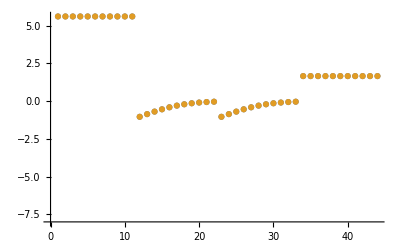

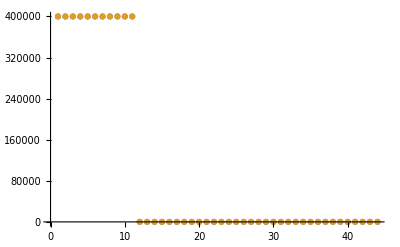

```mathematica
dataSetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

```mathematica
enzymeModel
```

```mathematica
filteredDataList[[1,2]]
rateConstsSub[[All,2]]/.Reverse/@rateConstsSub
```

{7.45715,2.33036×10^7,7.81223×10^8,1059.5,2.19268×10^8,5.37755×10^7,7.73533×10^8,9.95865×10^8,6.57888×10^8,2.78554×10^8,6.98062×10^8,5.56889×10^8}

{k_GAPD1^⟵,k_GAPD1^⟶,k_GAPD2^⟵,k_GAPD2^⟶,k_GAPD3^⟵,k_GAPD3^⟶,k_GAPD4^⟵,k_GAPD4^⟶,k_GAPD5^⟵,k_GAPD5^⟶,k_GAPD6^⟵,k_GAPD6^⟶}

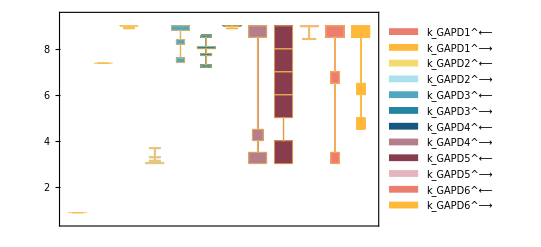

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

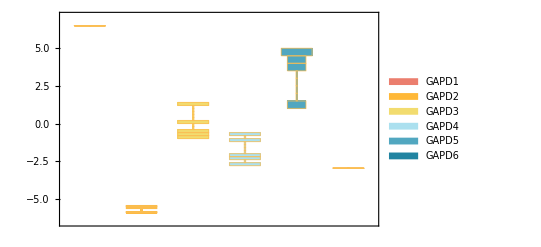

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

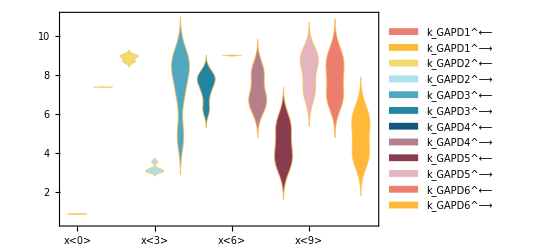

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

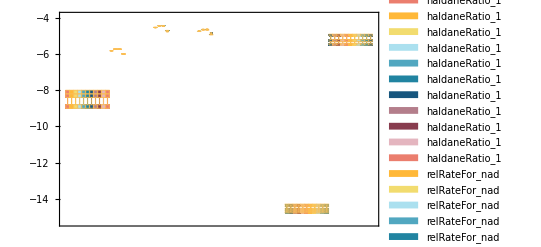

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000045 | 0.000044999 | 0.00221251
0.00089 | 0.000889609 | 0.043892
0.00053 | 0.000529863 | 0.0259263

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
1059.36 | 1059.36 | 0.0000114381

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 2.37024×10^-7

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 2.37024×10^-7

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

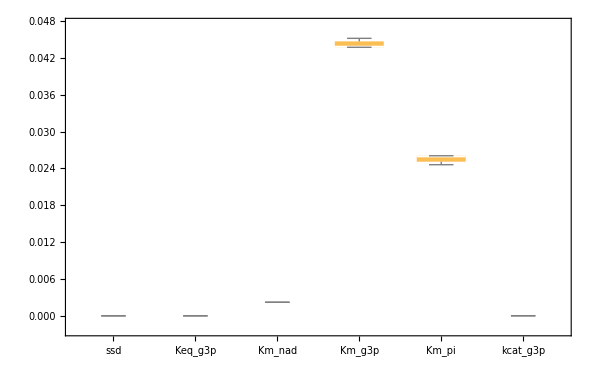

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```